```mathematica
Needs["VectorFieldPlots`"]
```

```mathematica
VectorFieldPlot[{1, 1, Sin[y]}, {t, -10, 10}, {y, -10, 10}, VectorPoints -> 25, VectorStyle -> Black, VectorScale -> {.02, 1, None}, Axes -> True, Frame -> False, AxesLabel -> {t, y}]
```

ListVectorFieldPlot::lpvf: ListVectorFieldPlot requires a rectangular array of vectors or a list of {base, vector} pairs.

ListVectorFieldPlot[{{{-10.,-10.},{1.,1.,0.544021}},{{-10.,-8.57143},{1.,1.,-0.753487}},{{-10.,-7.14286},{1.,1.,-0.757628}},{{-10.,-5.71429},{1.,1.,0.538705}},{{-10.,-4.28571},{1.,1.,0.910347}},{{-10.,-2.85714},{1.,1.,-0.280629}},{{-10.,-1.42857},{1.,1.,-0.989903}},{{-10.,0.},{1.,1.,0.}},{{-10.,1.42857},{1.,1.,0.989903}},{{-10.,2.85714},{1.,1.,0.280629}},{{-10.,4.28571},{1.,1.,-0.910347}},{{-10.,5.71429},{1.,1.,-0.538705}},{{-10.,7.14286},{1.,1.,0.757628}},{{-10.,8.57143},{1.,1.,0.753487}},{{-10.,10.},{1.,1.,-0.544021}},{{-8.57143,-10.},{1.,1.,0.544021}},{{-8.57143,-8.57143},{1.,1.,-0.753487}},{{-8.57143,-7.14286},{1.,1.,-0.757628}},{{-8.57143,-5.71429},{1.,1.,0.538705}},{{-8.57143,-4.28571},{1.,1.,0.910347}},{{-8.57143,-2.85714},{1.,1.,-0.280629}},{{-8.57143,-1.42857},{1.,1.,-0.989903}},{{-8.57143,0.},{1.,1.,0.}},{{-8.57143,1.42857},{1.,1.,0.989903}},{{-8.57143,2.85714},{1.,1.,0.280629}},{{-8.57143,4.28571},{1.,1.,-0.910347}},{{-8.57143,5.71429},{1.,1.,-0.538705}},{{-8.57143,7.14286},{1.,1.,0.757628}},{{-8.57143,8.57143},{1.,1.,0.753487}},{{-8.57143,10.},{1.,1.,-0.544021}},{{-7.14286,-10.},{1.,1.,0.544021}},{{-7.14286,-8.57143},{1.,1.,-0.753487}},{{-7.14286,-7.14286},{1.,1.,-0.757628}},{{-7.14286,-5.71429},{1.,1.,0.538705}},{{-7.14286,-4.28571},{1.,1.,0.910347}},{{-7.14286,-2.85714},{1.,1.,-0.280629}},{{-7.14286,-1.42857},{1.,1.,-0.989903}},{{-7.14286,0.},{1.,1.,0.}},{{-7.14286,1.42857},{1.,1.,0.989903}},{{-7.14286,2.85714},{1.,1.,0.280629}},{{-7.14286,4.28571},{1.,1.,-0.910347}},{{-7.14286,5.71429},{1.,1.,-0.538705}},{{-7.14286,7.14286},{1.,1.,0.757628}},{{-7.14286,8.57143},{1.,1.,0.753487}},{{-7.14286,10.},{1.,1.,-0.544021}},{{-5.71429,-10.},{1.,1.,0.544021}},{{-5.71429,-8.57143},{1.,1.,-0.753487}},{{-5.71429,-7.14286},{1.,1.,-0.757628}},{{-5.71429,-5.71429},{1.,1.,0.538705}},{{-5.71429,-4.28571},{1.,1.,0.910347}},{{-5.71429,-2.85714},{1.,1.,-0.280629}},{{-5.71429,-1.42857},{1.,1.,-0.989903}},{{-5.71429,0.},{1.,1.,0.}},{{-5.71429,1.42857},{1.,1.,0.989903}},{{-5.71429,2.85714},{1.,1.,0.280629}},{{-5.71429,4.28571},{1.,1.,-0.910347}},{{-5.71429,5.71429},{1.,1.,-0.538705}},{{-5.71429,7.14286},{1.,1.,0.757628}},{{-5.71429,8.57143},{1.,1.,0.753487}},{{-5.71429,10.},{1.,1.,-0.544021}},{{-4.28571,-10.},{1.,1.,0.544021}},{{-4.28571,-8.57143},{1.,1.,-0.753487}},{{-4.28571,-7.14286},{1.,1.,-0.757628}},{{-4.28571,-5.71429},{1.,1.,0.538705}},{{-4.28571,-4.28571},{1.,1.,0.910347}},{{-4.28571,-2.85714},{1.,1.,-0.280629}},{{-4.28571,-1.42857},{1.,1.,-0.989903}},{{-4.28571,0.},{1.,1.,0.}},{{-4.28571,1.42857},{1.,1.,0.989903}},{{-4.28571,2.85714},{1.,1.,0.280629}},{{-4.28571,4.28571},{1.,1.,-0.910347}},{{-4.28571,5.71429},{1.,1.,-0.538705}},{{-4.28571,7.14286},{1.,1.,0.757628}},{{-4.28571,8.57143},{1.,1.,0.753487}},{{-4.28571,10.},{1.,1.,-0.544021}},{{-2.85714,-10.},{1.,1.,0.544021}},{{-2.85714,-8.57143},{1.,1.,-0.753487}},{{-2.85714,-7.14286},{1.,1.,-0.757628}},{{-2.85714,-5.71429},{1.,1.,0.538705}},{{-2.85714,-4.28571},{1.,1.,0.910347}},{{-2.85714,-2.85714},{1.,1.,-0.280629}},{{-2.85714,-1.42857},{1.,1.,-0.989903}},{{-2.85714,0.},{1.,1.,0.}},{{-2.85714,1.42857},{1.,1.,0.989903}},{{-2.85714,2.85714},{1.,1.,0.280629}},{{-2.85714,4.28571},{1.,1.,-0.910347}},{{-2.85714,5.71429},{1.,1.,-0.538705}},{{-2.85714,7.14286},{1.,1.,0.757628}},{{-2.85714,8.57143},{1.,1.,0.753487}},{{-2.85714,10.},{1.,1.,-0.544021}},{{-1.42857,-10.},{1.,1.,0.544021}},{{-1.42857,-8.57143},{1.,1.,-0.753487}},{{-1.42857,-7.14286},{1.,1.,-0.757628}},{{-1.42857,-5.71429},{1.,1.,0.538705}},{{-1.42857,-4.28571},{1.,1.,0.910347}},{{-1.42857,-2.85714},{1.,1.,-0.280629}},{{-1.42857,-1.42857},{1.,1.,-0.989903}},{{-1.42857,0.},{1.,1.,0.}},{{-1.42857,1.42857},{1.,1.,0.989903}},{{-1.42857,2.85714},{1.,1.,0.280629}},{{-1.42857,4.28571},{1.,1.,-0.910347}},{{-1.42857,5.71429},{1.,1.,-0.538705}},{{-1.42857,7.14286},{1.,1.,0.757628}},{{-1.42857,8.57143},{1.,1.,0.753487}},{{-1.42857,10.},{1.,1.,-0.544021}},{{0.,-10.},{1.,1.,0.544021}},{{0.,-8.57143},{1.,1.,-0.753487}},{{0.,-7.14286},{1.,1.,-0.757628}},{{0.,-5.71429},{1.,1.,0.538705}},{{0.,-4.28571},{1.,1.,0.910347}},{{0.,-2.85714},{1.,1.,-0.280629}},{{0.,-1.42857},{1.,1.,-0.989903}},{{0.,0.},{1.,1.,0.}},{{0.,1.42857},{1.,1.,0.989903}},{{0.,2.85714},{1.,1.,0.280629}},{{0.,4.28571},{1.,1.,-0.910347}},{{0.,5.71429},{1.,1.,-0.538705}},{{0.,7.14286},{1.,1.,0.757628}},{{0.,8.57143},{1.,1.,0.753487}},{{0.,10.},{1.,1.,-0.544021}},{{1.42857,-10.},{1.,1.,0.544021}},{{1.42857,-8.57143},{1.,1.,-0.753487}},{{1.42857,-7.14286},{1.,1.,-0.757628}},{{1.42857,-5.71429},{1.,1.,0.538705}},{{1.42857,-4.28571},{1.,1.,0.910347}},{{1.42857,-2.85714},{1.,1.,-0.280629}},{{1.42857,-1.42857},{1.,1.,-0.989903}},{{1.42857,0.},{1.,1.,0.}},{{1.42857,1.42857},{1.,1.,0.989903}},{{1.42857,2.85714},{1.,1.,0.280629}},{{1.42857,4.28571},{1.,1.,-0.910347}},{{1.42857,5.71429},{1.,1.,-0.538705}},{{1.42857,7.14286},{1.,1.,0.757628}},{{1.42857,8.57143},{1.,1.,0.753487}},{{1.42857,10.},{1.,1.,-0.544021}},{{2.85714,-10.},{1.,1.,0.544021}},{{2.85714,-8.57143},{1.,1.,-0.753487}},{{2.85714,-7.14286},{1.,1.,-0.757628}},{{2.85714,-5.71429},{1.,1.,0.538705}},{{2.85714,-4.28571},{1.,1.,0.910347}},{{2.85714,-2.85714},{1.,1.,-0.280629}},{{2.85714,-1.42857},{1.,1.,-0.989903}},{{2.85714,0.},{1.,1.,0.}},{{2.85714,1.42857},{1.,1.,0.989903}},{{2.85714,2.85714},{1.,1.,0.280629}},{{2.85714,4.28571},{1.,1.,-0.910347}},{{2.85714,5.71429},{1.,1.,-0.538705}},{{2.85714,7.14286},{1.,1.,0.757628}},{{2.85714,8.57143},{1.,1.,0.753487}},{{2.85714,10.},{1.,1.,-0.544021}},{{4.28571,-10.},{1.,1.,0.544021}},{{4.28571,-8.57143},{1.,1.,-0.753487}},{{4.28571,-7.14286},{1.,1.,-0.757628}},{{4.28571,-5.71429},{1.,1.,0.538705}},{{4.28571,-4.28571},{1.,1.,0.910347}},{{4.28571,-2.85714},{1.,1.,-0.280629}},{{4.28571,-1.42857},{1.,1.,-0.989903}},{{4.28571,0.},{1.,1.,0.}},{{4.28571,1.42857},{1.,1.,0.989903}},{{4.28571,2.85714},{1.,1.,0.280629}},{{4.28571,4.28571},{1.,1.,-0.910347}},{{4.28571,5.71429},{1.,1.,-0.538705}},{{4.28571,7.14286},{1.,1.,0.757628}},{{4.28571,8.57143},{1.,1.,0.753487}},{{4.28571,10.},{1.,1.,-0.544021}},{{5.71429,-10.},{1.,1.,0.544021}},{{5.71429,-8.57143},{1.,1.,-0.753487}},{{5.71429,-7.14286},{1.,1.,-0.757628}},{{5.71429,-5.71429},{1.,1.,0.538705}},{{5.71429,-4.28571},{1.,1.,0.910347}},{{5.71429,-2.85714},{1.,1.,-0.280629}},{{5.71429,-1.42857},{1.,1.,-0.989903}},{{5.71429,0.},{1.,1.,0.}},{{5.71429,1.42857},{1.,1.,0.989903}},{{5.71429,2.85714},{1.,1.,0.280629}},{{5.71429,4.28571},{1.,1.,-0.910347}},{{5.71429,5.71429},{1.,1.,-0.538705}},{{5.71429,7.14286},{1.,1.,0.757628}},{{5.71429,8.57143},{1.,1.,0.753487}},{{5.71429,10.},{1.,1.,-0.544021}},{{7.14286,-10.},{1.,1.,0.544021}},{{7.14286,-8.57143},{1.,1.,-0.753487}},{{7.14286,-7.14286},{1.,1.,-0.757628}},{{7.14286,-5.71429},{1.,1.,0.538705}},{{7.14286,-4.28571},{1.,1.,0.910347}},{{7.14286,-2.85714},{1.,1.,-0.280629}},{{7.14286,-1.42857},{1.,1.,-0.989903}},{{7.14286,0.},{1.,1.,0.}},{{7.14286,1.42857},{1.,1.,0.989903}},{{7.14286,2.85714},{1.,1.,0.280629}},{{7.14286,4.28571},{1.,1.,-0.910347}},{{7.14286,5.71429},{1.,1.,-0.538705}},{{7.14286,7.14286},{1.,1.,0.757628}},{{7.14286,8.57143},{1.,1.,0.753487}},{{7.14286,10.},{1.,1.,-0.544021}},{{8.57143,-10.},{1.,1.,0.544021}},{{8.57143,-8.57143},{1.,1.,-0.753487}},{{8.57143,-7.14286},{1.,1.,-0.757628}},{{8.57143,-5.71429},{1.,1.,0.538705}},{{8.57143,-4.28571},{1.,1.,0.910347}},{{8.57143,-2.85714},{1.,1.,-0.280629}},{{8.57143,-1.42857},{1.,1.,-0.989903}},{{8.57143,0.},{1.,1.,0.}},{{8.57143,1.42857},{1.,1.,0.989903}},{{8.57143,2.85714},{1.,1.,0.280629}},{{8.57143,4.28571},{1.,1.,-0.910347}},{{8.57143,5.71429},{1.,1.,-0.538705}},{{8.57143,7.14286},{1.,1.,0.757628}},{{8.57143,8.57143},{1.,1.,0.753487}},{{8.57143,10.},{1.,1.,-0.544021}},{{10.,-10.},{1.,1.,0.544021}},{{10.,-8.57143},{1.,1.,-0.753487}},{{10.,-7.14286},{1.,1.,-0.757628}},{{10.,-5.71429},{1.,1.,0.538705}},{{10.,-4.28571},{1.,1.,0.910347}},{{10.,-2.85714},{1.,1.,-0.280629}},{{10.,-1.42857},{1.,1.,-0.989903}},{{10.,0.},{1.,1.,0.}},{{10.,1.42857},{1.,1.,0.989903}},{{10.,2.85714},{1.,1.,0.280629}},{{10.,4.28571},{1.,1.,-0.910347}},{{10.,5.71429},{1.,1.,-0.538705}},{{10.,7.14286},{1.,1.,0.757628}},{{10.,8.57143},{1.,1.,0.753487}},{{10.,10.},{1.,1.,-0.544021}}},{ScaleFactor→1.42857,VectorPoints→25,VectorStyle→GrayLevel[0],VectorScale→{0.02,1,None},Axes→True,Frame→False,AxesLabel→{t,y},AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorFunction→None,ColorOutput→Automatic,ContentSelectable→Automatic,Epilog→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},MaxArrowLength→None,Method→Automatic,PlotLabel→None,PlotPoints→Automatic,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScaleFactor→Automatic,ScaleFunction→None,Ticks→Automatic,TicksStyle→{},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm}]

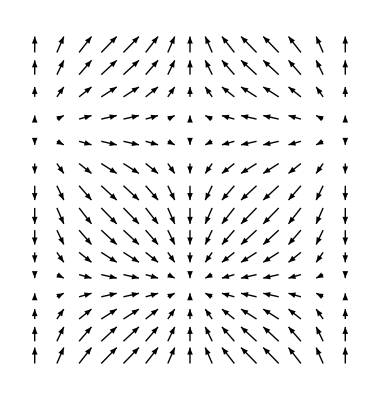

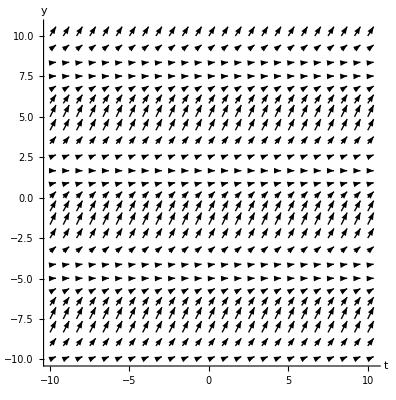

```mathematica
VectorFieldPlot[{Sin[x], Cos[y]}, {x, 0, 2Pi}, {y, 0, 2Pi}]
```

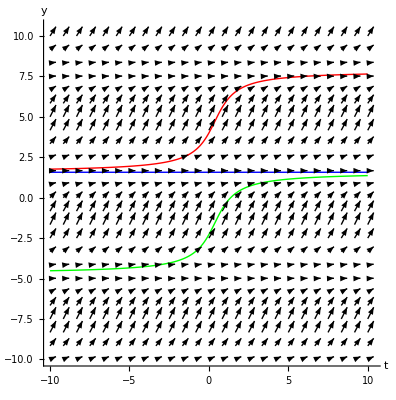

```mathematica
sol1=NDSolve[{y'[t]==1-Sin[y[t]],y[0]==4},y,{t,-10,10}];
plot1=Plot[y[t]/.sol1,{t,-10,10},PlotStyle->{Thick,Red}];
sol2=NDSolve[{y'[t]==1-Sin[y[t]],y[0]==4-2*Pi},y,{t,-10,10}];
plot2=Plot[y[t]/.sol2,{t,-10,10},PlotStyle->{Thick,Green}];
sol3=NDSolve[{y'[t]==1-Sin[y[t]],y[0]==Pi/2},y,{t,-10,10}];
plot3=Plot[y[t]/.sol3,{t,-10,10},PlotStyle->{Thick,Blue}];
Show[dir1,plot1,plot2,plot3,PlotRange->All]
```

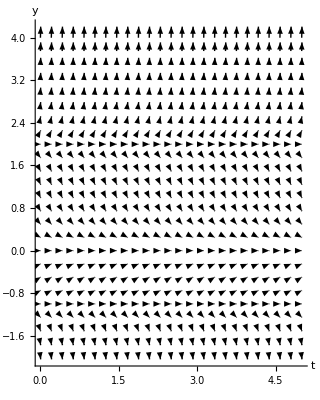

```mathematica
dir2 = VectorFieldPlot[{1, y*(y-2)*(y+1)}, {t, 0, 5}, {y, -2, 4}, PlotPoints -> 25, Axes -> True, AxesLabel -> {t, y}]
```

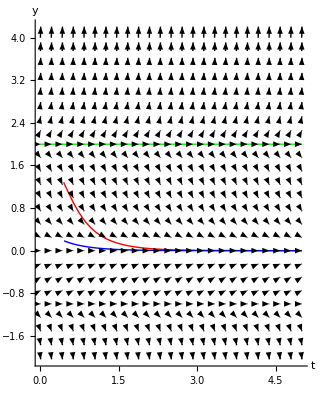

```mathematica
sol3=NDSolve[{y'[t]==y[t]*(y[t]-2)*(y[t]+1),y[0]==1.9},y,{t,0,5}];
plot3=Plot[y[t]/.sol3,{t,0,5},PlotStyle->{Thick,Red}];
sol4=NDSolve[{y'[t]==y[t]*(y[t]-2)*(y[t]+1),y[0]==2},y,{t,0,5}];
plot4=Plot[y[t]/.sol4,{t,0,5},PlotStyle->{Thick,Green}];
sol5=NDSolve[{y'[t]==y[t]*(y[t]-2)*(y[t]+1),y[0]==0.5},y,{t,0,5}];
plot5=Plot[y[t]/.sol5,{t,0,5},PlotStyle->{Thick,Blue}];
Show[dir2,plot3,plot4,plot5,PlotRange->All]
```